```mathematica
xmin=-2;
xmax=6;
ymin=-2;
ymax=2;
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1
SetDirectory["/home/brady/SU2/Results/Square_Cylinder"];
data=Import["surface_flow_00008.csv"];
shapedata=data[[2;;-1,{2,3}]];
shape=Graphics[{Gray,Polygon[shapedata]}];
datafile=ReadList[Export[".dat",Import["flow_00008.dat"][[4;;-1]]],Number,RecordLists->True,RecordSeparators->{"\n"}];
DeleteFile[".dat"]
Do[If[Dimensions[datafile[[i]]][[1]]==4,{CleanData=datafile[[1;;i-1]],Break[]}],{i,1,Dimensions[datafile][[1]]}];
Test=CleanData[[All,1;;6]];

stream={};
Velocity = {};
Do[{
If[Test[[i,1]]>xmin&&Test[[i,1]]<xmax&&Test[[i,2]]>ymin&&Test[[i,2]]<ymax,AppendTo[stream,{{Test[[i,1]],Test[[i,2]]},{Test[[i,4]]/Test[[i,3]],Test[[i,5]]/Test[[i,3]]}}]];
AppendTo[Velocity,{Test[[i,1]],Test[[i,2]],√((Test[[i,4]]/Test[[i,3]])^2+(Test[[i,5]]/Test[[i,3]])^2)}]},{i,1,Length[Test]}]
```

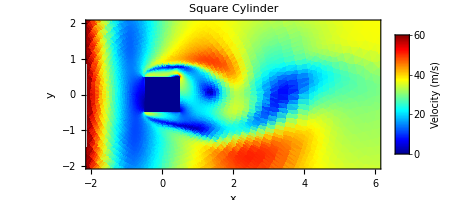

```mathematica
velplot = ListDensityPlot[Velocity,ColorFunction->jet,PlotRange->{{xmin,xmax},{ymin,ymax},{0,60}},AspectRatio->Automatic,PlotLegends->BarLegend[Automatic,LegendLabel->"Velocity (m/s)",LabelStyle->{FontFamily->"Times"}],FrameLabel->{"x","y"},PlotLabel->"Square Cylinder",ImageSize->Full]
```

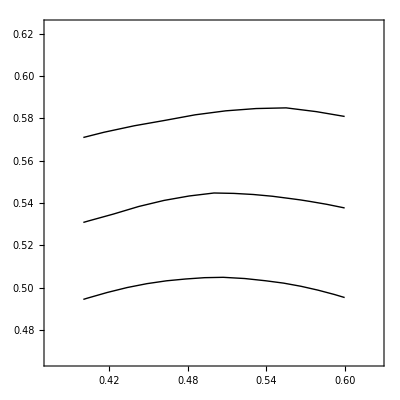

```mathematica
streamplot=ListStreamPlot[stream,StreamPoints->{Automatic,0.05},StreamScale->Full,StreamStyle->{Arrowheads[0],Black},PerformanceGoal->"Quality"]
```

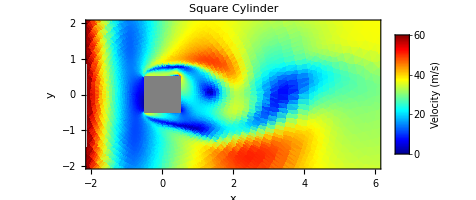

```mathematica
VelocityFull=Show[velplot,shape]
```

```mathematica
Export["Square_Cylinder08.pdf",VelocityFull]
Export["Square_Cylinder08.png",VelocityFull]
```

Square_Cylinder08.pdf

Square_Cylinder08.png